```mathematica
ClearAll["Global`*"]
Sm = 1/Δ *{0, 0, -1/4, -5/6, 3/2, -1/2, 1/12};
Sp = 1/Δ *{-1/12, 1/2, -3/2, 5/6, 1/4, 0, 0};

Ez = {Sin[-w*t - 3*k*Δ], Sin[-w*t - 2*k*Δ], Sin[-w*t -k*Δ],Sin[-w*t],Sin[-w*t + k*Δ], Sin[-w*t + 2*k*Δ], Sin[-w*t + 3*k*Δ]} ;
By:=-Ez;
sum1= Ez[[4]]Dot[By,Sp];
sum2= By[[4]]Dot[Ez,Sp];
sum3= Dot[Ez *By, Sp]
```

-(5 Sin[t w]^2)/(6 Δ)-Sin[t w-k Δ]^2/(4 Δ)+(3 Sin[t w+k Δ]^2)/(2 Δ)-Sin[t w+2 k Δ]^2/(2 Δ)+Sin[t w+3 k Δ]^2/(12 Δ)

```mathematica
sum1 + sum2 + sum3
```

-(5 Sin[t w]^2)/(6 Δ)-Sin[t w-k Δ]^2/(4 Δ)+(3 Sin[t w+k Δ]^2)/(2 Δ)-Sin[t w+2 k Δ]^2/(2 Δ)+Sin[t w+3 k Δ]^2/(12 Δ)-Sin[t w] ((5 Sin[t w])/(6 Δ)+Sin[t w-k Δ]/(4 Δ)-(3 Sin[t w+k Δ])/(2 Δ)+Sin[t w+2 k Δ]/(2 Δ)-Sin[t w+3 k Δ]/(12 Δ))+Sin[t w] (-(5 Sin[t w])/(6 Δ)-Sin[t w-k Δ]/(4 Δ)+(3 Sin[t w+k Δ])/(2 Δ)-Sin[t w+2 k Δ]/(2 Δ)+Sin[t w+3 k Δ]/(12 Δ))

```mathematica
w = 1/2;
Element[t,Reals]
k =1/2;
Δ =1/8;
```

t∈ℝ

```mathematica
sum1 + sum2 + sum3;
N[sum1 + sum2 + sum3]
w*Cos[-w*t] - Dot[Ez,Sp]
```

-2. Sin[0.0625-0.5 t]^2+12. Sin[0.0625+0.5 t]^2-4. Sin[0.125+0.5 t]^2+0.666667 Sin[0.1875+0.5 t]^2+(2. Sin[0.0625-0.5 t]+12. Sin[0.0625+0.5 t]-4. Sin[0.125+0.5 t]+0.666667 Sin[0.1875+0.5 t]-6.66667 Sin[0.5 t]) Sin[0.5 t]-6.66667 Sin[0.5 t]^2-1. Sin[0.5 t] (-2. Sin[0.0625-0.5 t]-12. Sin[0.0625+0.5 t]+4. Sin[0.125+0.5 t]-0.666667 Sin[0.1875+0.5 t]+6.66667 Sin[0.5 t])

1/2 Cos[t/2]-2 Sin[1/16-t/2]-12 Sin[1/16+t/2]+4 Sin[1/8+t/2]-2/3 Sin[3/16+t/2]+20/3 Sin[t/2]

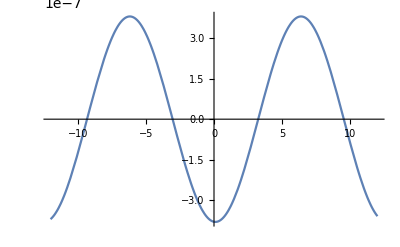

```mathematica
Plot[w*Cos[-w*t] - Dot[Ez,Sm], {t,-12, 12}]
```

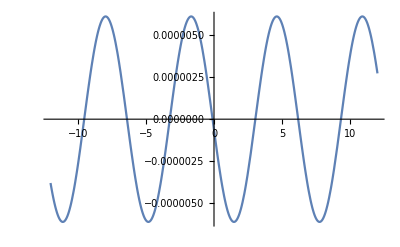

```mathematica
Plot[-2w*Sin[-w*t]Cos[-w*t]+Dot[Ez^2,Sp], {t, -12, 12}]
```

```mathematica
Sms1 = 1/Δ *{0,0,-16/60,-45/60,80/60,-20/60,1/60};
Sms2 = 1/Δ *{0,0,-75/240,-128/240,225/240,-25/240,3/240};
Sms3 = 1/Δ *{0,0,-192/210,+35/210,1,-63/210,10/210}/2;
Sps1 =1/Δ *{-8/30,45/30,-120/30,80/30,3/30,0,0}/2;
Sps2 = 1/Δ *{-15/30,64/30,-90/30,35/30,6/30,0,0}/2;
Sps3 = 1/Δ *{-64/210,175/210,-350/210,189/210,50/210,0,0}/2;
```

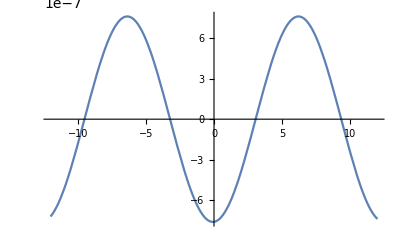

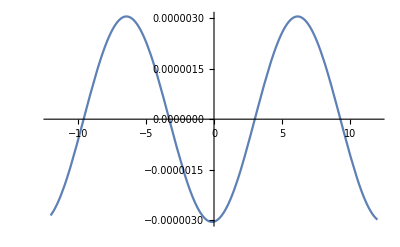

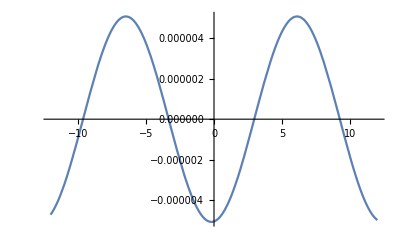

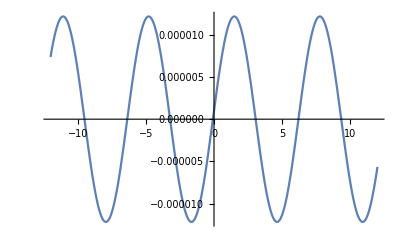

```mathematica
Ez1 = {Sin[-w*t - 3*k*Δ], Sin[-w*t - 2*k*Δ], Sin[-w*t -k*Δ],Sin[-w*t],Sin[-w*t + k*Δ], Sin[-w*t + 2*k*Δ], Sin[-w*t + 4*k*Δ]} ;
Ez2 = {Sin[-w*t - 3*k*Δ], Sin[-w*t - 2*k*Δ], Sin[-w*t -k*Δ],Sin[-w*t],Sin[-w*t + k*Δ], Sin[-w*t + 3*k*Δ], Sin[-w*t + 5*k*Δ]} ;
Ez3 = {Sin[-w*t - 3*k*Δ], Sin[-w*t - 2*k*Δ], Sin[-w*t -k*Δ],Sin[-w*t],Sin[-w*t + 2*k*Δ], Sin[-w*t + 4*k*Δ], Sin[-w*t + 6*k*Δ]} ;
Ez4 = {Sin[-w*t - 4*k*Δ], Sin[-w*t - 3*k*Δ], Sin[-w*t -2k*Δ],Sin[-w*t],Sin[-w*t + 2*k*Δ], Sin[-w*t + 4*k*Δ], Sin[-w*t + 6*k*Δ]} ;
Ez5 = {Sin[-w*t - 5*k*Δ], Sin[-w*t - 4*k*Δ], Sin[-w*t -2k*Δ],Sin[-w*t],Sin[-w*t + 2*k*Δ], Sin[-w*t + 4*k*Δ], Sin[-w*t + 6*k*Δ]} ;
Ez6 = {Sin[-w*t - 6*k*Δ], Sin[-w*t - 4*k*Δ], Sin[-w*t -2k*Δ],Sin[-w*t],Sin[-w*t + 2*k*Δ], Sin[-w*t + 4*k*Δ], Sin[-w*t + 6*k*Δ]} ;
By1:=-Ez1;
By2:=-Ez2;
By3:=-Ez3;
By4:=-Ez4;
By5:=-Ez5;
By6:=-Ez6;

Plot[w*Cos[-w*t] - Dot[Ez3,Sps1], {t,-12, 12}]
Plot[w*Cos[-w*t] - Dot[Ez4,Sps2], {t,-12, 12}]
Plot[w*Cos[-w*t] - Dot[Ez5,Sps3], {t,-12, 12}]
```